```mathematica
Clear["Global`*"]
```

```mathematica
r=0.64;
l=1.5;
mc=0.3;
oc=0.15;
ot=oc*0.15;
mt=(0.108+ot)/2;
margin=0.03;
os=0.009;
ms=0.006;
β=π/12;
mrc=mc/3;
orc=oc/4;
mmrc=orc;
m=1;
maxγ=π/3;
g=9.82;
CSm=50/1000;
bodym=(450-260)/1000;
servom=6.5/1000+4/1000;
batterym=265/1000;
electronicsm=(320-260)/1000;
bodycm={0,mc/2-0.14};
batterycm={0,mc/2-battl/2-lidt};
motorm=54/1000;
motorcm={-0.2,mc/2};
eservocm={-0.17,0};
rservocm={-0.55,0};
propellerm=12/1000;
propellercm={0,0.02}+motorcm;
electronicsw=0.053;
electronicsh=0.025;
lidt=0.013;
battl=0.048;
batth=0.022;
glueRatio=0.3;(*glue, cabeling, etc adds an additional 20% mass*)
```

```mathematica
θ=ArcTan[-(-mc/2+ms-(-oc/2+os)),l/2-margin];
α=αx/.Solve[{Sin[θ]Sin[αx]-Cos[αx]Cos[maxγ]Cos[θ]==0,π>αx>0},αx][[1]];
R=Sin[θ]/Sin[-β+θ]*mmrc;
eL=Norm[{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)-{0,-mc/2+ms}];
rL=Norm[{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)-{l/2-margin,-oc/2+os}];
```

```mathematica
eCS={{0,-mc/2+ms},
{0,-mc/2+ms}+{Cos[θ+α],-Sin[θ+α]}*mrc/Cos[α],
{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)+{Cos[θ+β],-Sin[θ+β]}*R,
{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)};
rCS={{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r),
{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)+{Cos[θ-β],-Sin[θ-β]}*mmrc/Cos[β],
{l/2-margin,-oc/2+os}+{Cos[θ+β],-Sin[θ+β]}*orc/Cos[β],
{l/2-margin,-oc/2+os}};
```

```mathematica
wing=Reverse[{{0,-mc/2+ms},{-l/2+margin,-oc/2+os},
{0,-mc/2}*margin/l*2+{-l/2,-oc/2}*(1-margin/l*2),
{-l/2,-oc/2},{-l/2,oc/2},{0,mc/2},{l/2,oc/2},{l/2,-oc/2},{0,-mc/2}*margin/l*2+{l/2,-oc/2}*(1-margin/l*2),{l/2-margin,-oc/2+os},{0,-mc/2+ms}
}];
```

```mathematica
Area[n_List]:=Total[Det/@Partition[n,2,1,{1,1}]]/2
CenterOfMass[n_List]:=Module[{x,y,m,det,dx,dy},m=Partition[n,2,1,{1,1}];
det=Det/@m;
dx=Last[#]+First[#]&/@m[[All,All,1]];
dy=Last[#]+First[#]&/@m[[All,All,2]];
x=Total[det dx];
y=Total[det dy];
1/(6Area[n]){x,y}]
```

```mathematica
flip[p_]:={{-1,0},{0,1}}.p
```

```mathematica
eA=Area[eCS];
rA=Area[rCS];
wA=Area[wing];
tA=wA+2rA+2eA;
ecm=CenterOfMass[eCS];
rcm=CenterOfMass[rCS];
```

```mathematica
p={flip[rcm],flip[ecm], ecm, rcm};
A={rA,eA,eA,rA};
```

```mathematica
naca[t_,c_,x_]:=5t c(0.2969Sqrt[x/c]-0.1260(x/c)-0.3537(x/c)^2+0.2843(x/c)^3-0.1015(x/c)^4);
```

```mathematica
electronicscm={0,mc/2+electronicsw/2-x/.Solve[{naca[mt/mc,mc,x]==(electronicsh+0.005)/2,mc/2<x<mc},x][[1]],0};
ξ=ArcTan[-D[naca[mt/mc,mc,x],x]/.x->mc/2-electronicscm[[2]]];electronicscm=electronicscm+{0,0,-0.005/2-electronicsw*Sin[ξ]/2};
```

```mathematica
rm=CSm rA/(2rA+2eA);
```

```mathematica
em=CSm eA/(2rA+2eA);
```

```mathematica
masses={bodym,batterym,servom,servom,servom,servom,rm,rm,em,em,electronicsm,motorm, motorm,propellerm,propellerm}*(1+glueRatio);
```

```mathematica
totalm=Total[masses];
```

```mathematica
cms={bodycm,batterycm,rservocm,flip[rservocm],eservocm,flip[eservocm],rcm,flip[rcm],ecm,flip[ecm],electronicscm,motorcm,flip[motorcm],propellercm,flip[propellercm]};
cms=Table[If[Length[i]==2,i~Join~{0},i],{i,cms}];
```

```mathematica
cm=masses .cms/totalm
```

{0.,0.0559907,-0.000579065}

```mathematica
erM=Transpose[Table[(p[[j]]-{cm[[1]],cm[[2]]})*A[[j]],{j,1,4}]];
```

```mathematica
nv=NullSpace[erM];
```

```mathematica
nv4=Table[Normalize[i]*Sign[Total[i]],{i,{nv[[1]]-nv[[2]]nv[[1]][[4]]/nv[[2]][[4]],
       nv[[2]]-nv[[1]]nv[[2]][[1]]/nv[[1]][[1]]}}];
```

```mathematica
sym=Normalize[nv4[[1]]+nv4[[2]]];
asym=Normalize[nv4[[1]]-nv4[[2]]];
```

```mathematica
skew=nv4[[1]];
brake=sym;
pitch=Normalize[({1,1,1,1}-t*sym)/.Minimize[
({1,1,1,1}-t*sym).DiagonalMatrix[A].({1,1,1,1}-t*sym)
,t][[2]][[1]]];
roll=Normalize[({-1,-1,1,1}-t*asym)/.Minimize[
({-1,-1,1,1}-t*asym).DiagonalMatrix[A].({-1,-1,1,1}-t*asym)
,t][[2]][[1]]];
```

```mathematica
Grid[{{"","CS 1","CS 2","CS 3","CS 4"},{"skew"}~Join~skew,{"brake"}~Join~brake,{"pitch"}~Join~pitch,{"roll"}~Join~roll},Frame->All]
```

| CS 1 | CS 2 | CS 3 | CS 4
skew | 0.838293 | -0.464059 | 0.286208 | 0.
brake | 0.691711 | -0.146753 | -0.146753 | 0.691711
pitch | 0.411553 | 0.574999 | 0.574999 | 0.411553
roll | -0.67125 | -0.222314 | 0.222314 | 0.67125

```mathematica
A
```

{0.00940007,0.0317123,0.0317123,0.00940007}

```mathematica
DiagonalMatrix[Transpose[p][[2]]]
```

{{-0.0984319,0.,0.,0.},{0.,-0.15976,0.,0.},{0.,0.,-0.15976,0.},{0.,0.,0.,-0.0984319}}

```mathematica
Grid[{
{"","Moment"},
{"pitch",-pitch.DiagonalMatrix[Transpose[p][[2]]].A},
{"roll",roll.DiagonalMatrix[Transpose[p][[1]]].A}
},Frame->All]
```

| Moment
pitch | 0.00658789
roll | 0.0102422

```mathematica
Grid[{{"Outer CS area","Inner CS area","Total CS area"},{2rA,2eA,2rA+2eA}/tA},Frame->All]
```

Outer CS area | Inner CS area | Total CS area
0.0462187 | 0.155925 | 0.202143

```mathematica
Grid[{{"Outer length","Outer width","Inner length","Inner width"},{rL,orc,eL,mrc}},Frame->All]
```

Outer length | Outer width | Inner length | Inner width
0.260717 | 0.0375 | 0.463496 | 0.1

```mathematica
skewEffiency=-skew.DiagonalMatrix[A*Transpose[p][[1]]].skew/
(skew.skew)
```

0.00474342

```mathematica
ListLinePlot[{{0.1,0.0016495198397913826},{0.2,0.0001980694287184984},{0.4,0.0019152542579542044},{0.5,0.0034911129021768673},{0.6,0.004635749333239049},{0.63,0.00475333205141244},{0.64,0.004765191360971644},{0.65,0.0047634088890852674},{0.66,0.004748168115114836},{0.7,0.004635749333239049},{0.8,0.0033829341649519603},{0.9,0.0016495198397913826}},PlotMarkers->Automatic]
```

-Graphics-

```mathematica
getx[ru_,pu_,sm_]:=x/.NSolve[-(x skew+ru roll+pu pitch).DiagonalMatrix[A*Transpose[p][[1]]].(x skew+ru roll+pu pitch)==sm,x,Reals][[2]]
```

```mathematica
getx[rx_,px_,sx_]:=(rx roll+px pitch+t1 sym+t2 asym)/.Minimize[{(rx roll+px pitch+t1 sym+t2 asym).DiagonalMatrix[A].(rx roll+px pitch+t1 sym+t2 asym),

(rx roll+px pitch+t1 sym+t2 asym).DiagonalMatrix[A*Transpose[p][[1]]].(rx roll+px pitch+t1 sym+t2 asym)+sx==0},{t1,t2}][[2]]
```

```mathematica
Manipulate[BarChart[getx[r,p,s],PlotRange->{-2,2}],
{{s,0},-0.01,0.01},{{r,0},-1,1},{{p,0},-1,1},{{b,0},0,1}
]
```

```mathematica
Grid[{{"Mass [kg]",totalm},{"Max Speed [km/h]",Sqrt[g 2.0/(1.2*tA*0.015)]*3.6},{"Min Speed [km/h]",Sqrt[totalm g/(0.5 tA 1.2)]*3.6}},Frame->All]
```

Mass [kg] | 0.9607
Max Speed [km/h] | 186.451
Min Speed [km/h] | 22.3823

```mathematica
pc=Integrate[(mc/2-x(mc-oc)/2-0.25((1-x)(mc+mrc)+x(oc+orc)))((1-x)(mc+mrc)+x(oc+orc)),{x,0,1}]/Integrate[((1-x)(mc+mrc)+x(oc+orc)),{x,0,1}];
```

```mathematica
PieChart[{bodym,CSm,batterym,2 motorm+2propellerm,4servom,electronicsm},ChartLabels->{"body","control\n surfaces","battery","motors","servos","electronics"}]
```

-Graphics-

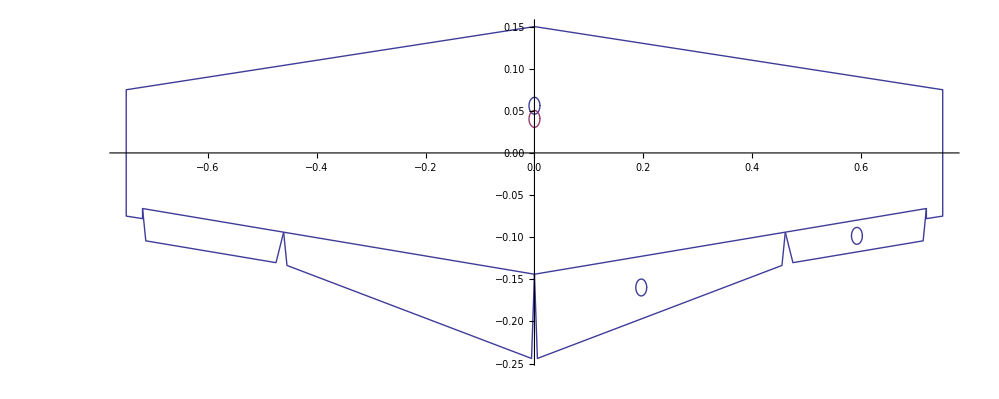

```mathematica
Show[
ListLinePlot[wing],
ListLinePlot[Table[flip[i],{i,eCS}]],
ListLinePlot[Table[flip[i],{i,rCS}]],
ListLinePlot[eCS],
ListLinePlot[rCS],
ListLinePlot[Table[ecm+0.01*{Cos[2π i/100],Sin[2π i/100]},{i,0,101}]],
ListLinePlot[Table[rcm+0.01*{Cos[2π i/100],Sin[2π i/100]},{i,0,101}]],
ListLinePlot[{Table[{cm[[1]],cm[[2]]}+0.01*{Cos[2π i/100],Sin[2π i/100]},{i,0,101}],Table[{0,pc}+0.01*{Cos[2π i/100],Sin[2π i/100]},{i,0,101}]}],
AspectRatio->Automatic,PlotRange->All
]
```

```mathematica
BT=Sum[masses[[i]]((cms[[i]]-cm).(cms[[i]]-cm)*IdentityMatrix[3]-KroneckerProduct[(cms[[i]]-cm),(cms[[i]]-cm)]),{i,1,Length[masses]}]+{{0.04^2+((oc+mc)/2)^2,0,0},{0,0.04^2+l^2,0},{0,0,l^2+((oc+mc)/2)^2}}*bodym/12;
```

```mathematica
BT//MatrixForm
```

(0.00798629 | 0. | 0.
0. | 0.0587106 | -0.0000632374
0. | -0.0000632374 | 0.0666389)

```mathematica
Eigensystem[BT]
```

{{0.0666395,0.0587101,0.00798629},{{0.,-0.00797536,0.999968},{0.,0.999968,0.00797536},{1.,0.,0.}}}

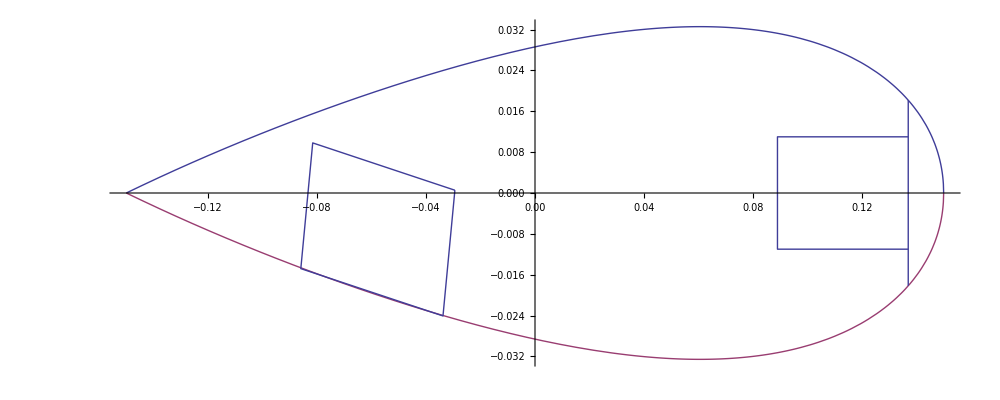

```mathematica
Show[{
Plot[{naca[mt/mc,mc,mc/2-x],-naca[mt/mc,mc,mc/2-x]},{x,-mc/2,mc/2}],
ListLinePlot[Table[{electronicscm[[2]],electronicscm[[3]]},{i,5}]+{{electronicsw/2,electronicsh/2},{-electronicsw/2,electronicsh/2},{-electronicsw/2,-electronicsh/2},{electronicsw/2,-electronicsh/2},{electronicsw/2,electronicsh/2}}.{{Cos[ξ],-Sin[ξ]},{Sin[ξ],Cos[ξ]}}]
,
ListLinePlot[{{mc/2-lidt,batth/2},{mc/2-battl-lidt,batth/2},{mc/2-battl-lidt,-batth/2},{mc/2-lidt,-batth/2}}],ListLinePlot[{{mc/2-lidt,naca[mt/mc,mc,lidt]},{mc/2-lidt,-naca[mt/mc,mc,lidt]}}]
},AspectRatio->Automatic]
```

```mathematica
ArcTan[D[naca[mt/mc,mc,mc/2-x],x]/.x->electronicscm[[2]]]
```

0.175701

```mathematica
screwLength1=x/Sin[ξ]/.Solve[{-naca[mt/mc,mc,mc/2-electronicscm[[2]]+electronicsw/2*Cos[ξ]+electronicsh/2*Sin[ξ]]+x /Tan[ξ]==naca[mt/mc,mc,mc/2-electronicscm[[2]]+electronicsw/2*Cos[ξ]+electronicsh/2*Sin[ξ]-x],0<x<0.1},x][[1]]
```

0.0308346

```mathematica
screwLength2=x/Sin[ξ]/.Solve[{-naca[mt/mc,mc,mc/2-electronicscm[[2]]-electronicsw/2*Cos[ξ]+electronicsh/2*Sin[ξ]]+x /Tan[ξ]==naca[mt/mc,mc,mc/2-electronicscm[[2]]-electronicsw/2*Cos[ξ]+electronicsh/2*Sin[ξ]-x],0<x<0.1},x][[1]]
```

0.0500661

```mathematica
Solve[{naca[mt/mc,mc,mc-x]==0.003/2,0<x<mc/2},x]
```

{{x→0.00586399}}

```mathematica
{electronicscm[[2]],electronicscm[[3]]}+{electronicsw/2,electronicsh/2}.{{Cos[ξ],-Sin[ξ]},{Sin[ξ],Cos[ξ]}}-{-mc/2,0}
```

{0.120594,0.000543264}

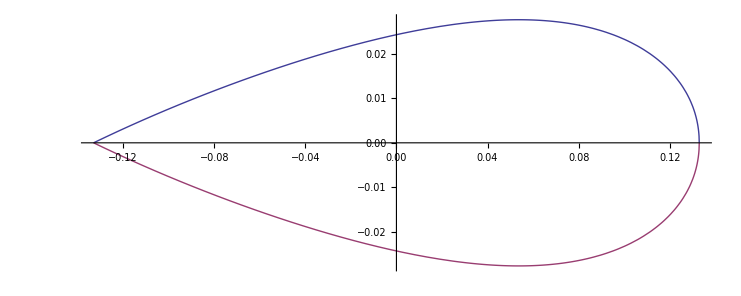

```mathematica
lr=-eservocm[[1]]/(l/2);
lc=mc (1-lr)+oc lr;
Show[{
Plot[{naca[(lr ot+(1-lr)mt)/lc,lc,lc/2-x],-naca[(lr ot+(1-lr)mt)/lc,lc,lc/2-x]},{x,-lc/2,lc/2}]
},AspectRatio->Automatic]
```

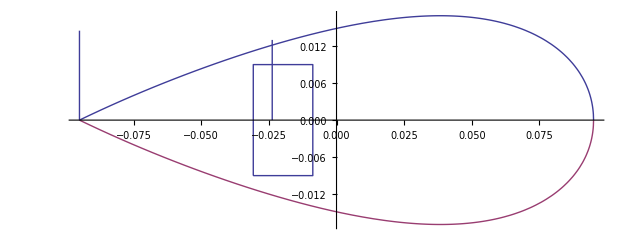

```mathematica
lr=-rservocm[[1]]/(l/2);
lc=mc (1-lr)+oc lr;
servoh=0.018;
servow=0.022;
servoy=0.015+servow/2+x/.Solve[{naca[(lr ot+(1-lr)mt)/lc,lc,lc/2-x]==servoh/2,-lc/2<x<0},x][[1]];
Show[{
Plot[{naca[(lr ot+(1-lr)mt)/lc,lc,lc/2-x],-naca[(lr ot+(1-lr)mt)/lc,lc,lc/2-x]},{x,-lc/2,lc/2}],
ListLinePlot[{{servoy-servow/2,-servoh/2},{servoy+servow/2,-servoh/2},{servoy+servow/2,servoh/2},{servoy-servow/2,servoh/2},{servoy-servow/2,-servoh/2}}],ListLinePlot[{{servoy-0.004,0},{servoy-0.004,0.013}}],
ListLinePlot[{{-lc/2,0},{-lc/2,0.0145}}]
},AspectRatio->Automatic]
```

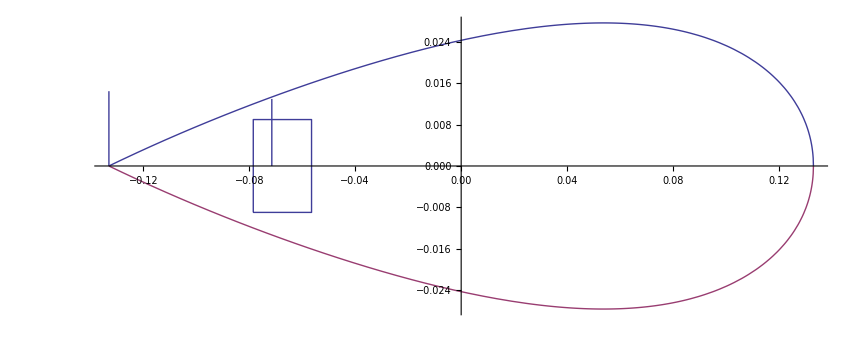

```mathematica
lr=-eservocm[[1]]/(l/2);
lc=mc (1-lr)+oc lr;
servoh=0.018;
servow=0.022;
servoy=0.015+servow/2+x/.Solve[{naca[(lr ot+(1-lr)mt)/lc,lc,lc/2-x]==servoh/2,-lc/2<x<0},x][[1]];
Show[{
Plot[{naca[(lr ot+(1-lr)mt)/lc,lc,lc/2-x],-naca[(lr ot+(1-lr)mt)/lc,lc,lc/2-x]},{x,-lc/2,lc/2}],
ListLinePlot[{{servoy-servow/2,-servoh/2},{servoy+servow/2,-servoh/2},{servoy+servow/2,servoh/2},{servoy-servow/2,servoh/2},{servoy-servow/2,-servoh/2}}],ListLinePlot[{{servoy-0.004,0},{servoy-0.004,0.013}}],
ListLinePlot[{{-lc/2,0},{-lc/2,0.0145}}]
},AspectRatio->Automatic]
```